## Initialization

### Package dependencies

```mathematica
Needs["RBSFA`",NotebookDirectory[]<>"Packages/RB-SFA.m"]
Print[$RBSFAversion]
Print[$MachineName]
```

RB-SFA v2.1.2, Thu 3 Nov 2016 15:44:57

ocelote

```mathematica
Needs["MaTeX`",NotebookDirectory[]<>"Packages/MaTeX.m"]
SetOptions[MaTeX,"Preamble"->{"\\usepackage{lmodern} "}];
```

```mathematica
$OutputDirectory=NotebookDirectory[]<>"../8-Spin-HHG/Figures/";
```

### Automatically save a copy with no output

To turn it on:

```mathematica
SetOptions[
EvaluationNotebook[],
NotebookEventActions->{
{"MenuCommand","Save"}:>(
NotebookSave[];
Block[{nb,tempfile,cleanfile},
tempfile=FileNameJoin[{NotebookDirectory[],"temp.nb"}];
cleanfile=FileNameJoin[{DirectoryName[#],"Clean",StringReplace[FileNameTake[#],{".nb"->" - clean.nb"}]}]&[NotebookFileName[]];
CopyFile[NotebookFileName[],tempfile];
nb=NotebookOpen[tempfile,Visible->False];
NotebookFind[nb,"Output",All,CellStyle];
NotebookDelete[nb];
NotebookSave[nb,cleanfile];
NotebookClose[nb];
Run["sed -i 's/Visible->True/Visible->True/g' ",StringReplace[cleanfile,{" "->"\\ ","\\"->"\\\\"}]];
DeleteFile[tempfile];
]
)
}
];
```

To turn it off:

```mathematica
SetOptions[EvaluationNotebook[],NotebookEventActions->{}]
```

## Figures

### Figure 8A - bicircular trefoil

#### Parameters

```mathematica
setFigure8Aparameters:={
samplepoints=1000;
numberofarrows=9;
n=7;
tlimit=π/3-0.05;
minOp=0.2;
δt=0.0001;
};
```

```mathematica
figure8AredCaption="Infrared driver
Right-circular polarization
800 nm";
figure8AblueCaption="Second harmonic
Left-circular polarization
400 nm";
```

#### Red inset

```mathematica
Block[{samplepoints,numberofarrows,n,tlimit,minOp,δt},
setFigure8Aparameters;

figure8AredInset=Show[{
ParametricPlot[
{Sin[t],Cos[t]}
,{t,-2π+tlimit,tlimit}
,Axes->None
,PlotStyle->Thick
,ColorFunctionScaling->False
,ColorFunction->Function[{x,y,t},Directive[Blend[{White,Red},If[t≥-tlimit,(t+tlimit)/(2tlimit)(1-minOp)+minOp,minOp]]]]
]
}~Join~
Table[
Graphics[{
Blend[{White,Red},If[t≥-tlimit,(t+tlimit)/(2tlimit)(1-minOp)+minOp,minOp]]
,Arrowheads[0.10]
,Arrow[{{Sin[t],Cos[t]},{Sin[t],Cos[t]}+0.2{Cos[t],-Sin[t]}}]
}]
,{t,{tlimit-0.15,0.1,-tlimit+0.2,-2π/3+0.1,-π,-4π/3}}]
~Join~
Table[
Graphics[{Thick,Blend[{White,Red},k/n(1-minOp)+minOp]
,Arrowheads[0.09],PointSize[0.02],Point[{0,0}]
,Arrow[{{0,0},{Sin[tlimit(2 k/n-1)],Cos[tlimit(2 k/n-1)]}}]
}]
,{k,0,n}
]
~Join~
Table[
Graphics[Inset[MaTeX["t_{"<>ToString[k+1]<>"}",FontSize->9],1.25{Sin[tlimit(2 k/n-1)],Cos[tlimit(2 k/n-1)]}]]
,{k,0,n}
]
,PlotRange->{1.2{-1,1},1.2{-1,1}}
,ImageSize->90
]
]
Style[figure8AredInset,Magnification->4]
```

#### Blue Inset

```mathematica
Block[{samplepoints,numberofarrows,n,tlimit,minOp,δt},
setFigure8Aparameters;

figure8AblueInset=Show[{
ParametricPlot[
{Sin[2t],-Cos[2t]}
,{t,-π+tlimit,tlimit}
,Axes->None
,PlotStyle->Thick
,ColorFunctionScaling->False
,ColorFunction->Function[{x,y,t},Directive[Blend[{White,Blue},If[t≥-tlimit,(t+tlimit)/(2tlimit)(1-minOp)+minOp,minOp]]]]
(*,ColorFunction->Function[{x,y,t},Directive[Opacity[If[t≥-tlimit,(t+tlimit)/(2tlimit)(1-minOp)+minOp,minOp]],Blue]]*)
]
}~Join~
Table[
Graphics[{Blend[{White,Blue},If[t≥-tlimit,(t+tlimit)/(2tlimit)(1-minOp)+minOp,minOp]]
,Arrowheads[0.10]
,Arrow[{{Sin[2t],-Cos[2t]},{Sin[2t],-Cos[2t]}+0.2{Cos[2t],Sin[2t]}}]
(*,Arrow[{{Sin[2t],-Cos[2t]},{Sin[2t+δt],-Cos[2t+δt]}}]*)
}]
,{t,{tlimit-0.1,0.05,-tlimit+0.17,-π/2}}]
~Join~
Table[Graphics[{Thick,Blend[{White,Blue},k/n(1-minOp)+minOp]
,Arrowheads[0.09],PointSize[0.02],Point[{0,0}]
,Arrow[{{0,0},{Sin[2tlimit(2 k/n-1)],-Cos[2tlimit(2 k/n-1)]}}]}]
,{k,0,n}
]
~Join~
Table[
Graphics[Inset[MaTeX["t_{"<>ToString[k+1]<>"}",FontSize->9],1.25{Sin[2tlimit(2 k/n-1)],-Cos[2tlimit(2 k/n-1)]}]]
,{k,0,n}
]
(*,ImageSize->500*)

,PlotRange->{1.2{-1,1},1.2{-1,1}}
,ImageSize->90
]
]
Style[figure8AblueInset,Magnification->4]
```

#### Full figure

```mathematica
Block[{samplepoints,numberofarrows,n,tlimit,minOp,δt,φ=4.5°},
setFigure8Aparameters;

figure8A=Show[{
ParametricPlot[
{Sin[t],Cos[t]}+{Sin[2t],-Cos[2t]}
,{t,0,2π}
,Axes->None
,PlotStyle->{Thick,Purple}
,Epilog->{
Inset[figure8AredInset,{-1.2,-0.7}],
Inset[figure8AblueInset,{1.2,-0.7}]
}
],
Table[
Graphics[{
Purple
,Arrowheads[0.06]
,Arrow[1.005{({Sin[t],Cos[t]}+{Sin[2t],-Cos[2t]})-0.01({Cos[t-φ],-Sin[t-φ]}+2{Cos[2t-2φ],Sin[2t-2φ]}),{Sin[t],Cos[t]}+{Sin[2t],-Cos[2t]}}]
}]
,{t,14°,2 π+0.3,(2 π)/numberofarrows}]
}
~Join~
Table[
Graphics[{Thick,Blend[{White,Red},(ta+tlimit)/(2tlimit)(1-minOp)+minOp],PointSize[0.0075],Point[{0,0}],Arrow[{{0,0},{Sin[ta],Cos[ta]}}]}]
,{ta,-tlimit,tlimit,2/n tlimit}
]
~Join~
Table[
Graphics[{Thick,Blend[{White,Blue},(ta+tlimit)/(2tlimit)(1-minOp)+minOp],PointSize[0.006],Point[{Sin[ta],Cos[ta]}],Arrow[{{Sin[ta],Cos[ta]},{Sin[ta],Cos[ta]}+{Sin[2ta],-Cos[2ta]}}]}]
,{ta,-tlimit,tlimit,2/n tlimit}
]
~Join~
Table[
Graphics[Inset[MaTeX["t_{"<>ToString[k+1]<>"}",FontSize->11],{Sin[tlimit(2 k/n-1)],Cos[tlimit(2 k/n-1)]}+1.1{Sin[2tlimit(2 k/n-1)],-Cos[2tlimit(2 k/n-1)]}]]
,{k,0,n}
]
~Join~{
Graphics[Text[Style[figure8AredCaption,FontFamily->"Latin Modern Math",9],{-1.3,-1.65}]],
Graphics[Text[Style[figure8AblueCaption,FontFamily->"Latin Modern Math",9],{1.3,-1.65}]]
}
,PlotRange->{1.9{-1,1},{-2,1.1}}
,ImageSize->300
,Frame->None
]
]
FileByteCount[Export[$OutputDirectory<>"figure8A.png",figure8A,ImageResolution->300]]
```

117110

### Figure 8C - bicircular APT

#### Parameters

```mathematica
figure8Cconditions:=Sequence[CarrierFrequency->0.057,TotalCycles->2,PointsPerCycle->300];
figure8Cparameters={F->√5 0.053,ω->0.057,HOcutoff->(3 8+1)};
```

#### Calculation

```mathematica
AbsoluteTiming[
figure8Cdipole=makeDipoleList[VectorPotential->Function[t,{F/ω Cos[ω t]/(√2),F/ω Sin[ω t]/(√2),0}+{F/(2ω)Cos[2ω t]/(√2),-F/(2ω)Sin[2ω t]/(√2),0}],FieldParameters->figure8Cparameters,figure8Cconditions];
]
```

{79.7267,Null}

#### Figure 8C

```mathematica
Block[{frequencyFilter,filteredDipole,points,maxNorm,HOmax},
HOmax=HOcutoff/.figure8Cparameters;

frequencyFilter=Join[#⟦1;;-2⟧,Reverse[#⟦1;;-2⟧]]&[If[#≥HOmax,1,0]&/@harmonicOrderAxis[figure8Cconditions]];
filteredDipole={-#⟦2⟧,#⟦1⟧}&/@Re[Transpose[Fourier/@Transpose[
frequencyFilter Transpose[Fourier/@Transpose[Re[figure8Cdipole⟦1;;-2⟧]]]
]]];
points=Join@@@Transpose[{
{#}&/@timeAxis[figure8Cconditions]⟦1;;-2⟧,
filteredDipole⟦1;;-1,{1,2}⟧
}];
maxNorm=1.1Max[Norm/@filteredDipole];

figure8C=Show[{
Graphics3D[{
Darker[Blue,0.2],Thickness[0.002],
Line[points]
}],
Graphics3D[{
GrayLevel[0.7],Thickness[0.002],
Line[({0,0,0}+{0,1,1}#)&/@points],
Line[({0,maxNorm,0}+{1,0,1}#)&/@points],
Line[({0,0,-maxNorm}+{1,1,0}#)&/@points]
}],
Graphics3D[{
Inset[MaTeX["\\omega t",FontSize->9],Scaled[{0.5,-.25,0}]],
Inset[MaTeX["D_x(t)",FontSize->9],Scaled[{-0.05,0.5,1.05}]],
Inset[MaTeX["D_y(t)",FontSize->9],Scaled[{-0.05,0.0,0.5}]]
}]
}
,BoxRatios->{3,1,1}
,ImageSize->600
,ViewPoint->3{1.3,-2.8,1.5}
,ViewVertical->{0, 0, 1}
,PlotRange->{timeAxis[figure8Cconditions]⟦{1,-1}⟧,maxNorm{-1,1},maxNorm{-1,1}}
]
]
```

```mathematica
FileByteCount[Export[$OutputDirectory<>"figure8C.pdf",Show[figure8C,ImageSize->350]]]
Export[$OutputDirectory<>"Figure8CParameters.tex",StringJoin[
"\\newcommand{\\figureEightCfield}{",ToString[F/.#],"} \n",
"\\newcommand{\\figureEightCintensity}{",ToString[FortranForm[SetPrecision[F/0.053 10^14/.#,3]]],"} \n",
"\\newcommand{\\figureEightCwavelength}{",ToString[Round[45.6/ω/.#]],"} \n",
"\\newcommand{\\figureEightCfrequency}{",ToString[F/.#],"} \n",
"\\newcommand{\\figureEightCcutoff}{",ToString[HOcutoff/.#],"}"
]&[figure8Cparameters],"Text"];
Import[%,"Text"]
```

52314

\newcommand{\figureEightCfield}{0.118512} 
\newcommand{\figureEightCintensity}{2.24e14} 
\newcommand{\figureEightCwavelength}{800} 
\newcommand{\figureEightCfrequency}{0.118512} 
\newcommand{\figureEightCcutoff}{25}

### Figure 8I - ellipses

#### Initialization

Computer and package conditions used in the calculation

```mathematica
Print[$MachineName]
Print[$RBSFAversion]
Print[$RBSFAcommit]
```

ramanujan

RB-SFA v2.1.1, Wed 8 Jun 2016 15:00:40

commit 2b1760d1bab5f0fcf0a85f5001ca9d1baab4d698
Author: Emilio Pisanty <pisanty@mbi-berlin.de>
Date:   Wed Jun 8 15:39:31 2016 +0200
    Fixes on Verbose returns
    
    Moved to Function[#1... ] for Verboseâ.86.923 to avoid shadowing problems. Fixed shadowing problems on Verboseâ.86.922.

#### Fields

```mathematica
bicircularA[t_]:=((F1/ω1{ Cos[t ω1] Sin[α],- Cos[α] Sin[t ω1]}+F2/ω2{Cos[β]Cos[ω2 t],Sin[β]Sin[ω2 t]})flatTopEnvelope[ω1,nTotal,envPower][t])
bicircularParameters={F1->0.075,F2->0.075,(*α->45°,*)β->45°,ω1->45.6/800,ω2->45.6/410,nTotal->10,envPower->4};
figure8Iconditions:=Sequence[TotalCycles->10,CarrierFrequency->45.6/800,PointsPerCycle->180,IntegrationPointsPerCycle->250];
```

Envelope in use:

```mathematica
Block[{ω1=1,nTotal=10,envPower=4},Plot[flatTopEnvelope[ω1,nTotal,envPower][t],{t,0,nTotal (2π)/ω1}]]
```

#### Calculation admin

```mathematica
Quit
```

```mathematica
Length[LaunchKernels[16-Length[Kernels[]]]]
```

16

```mathematica
Length[αRange=Range[0,90°,0.5°]]
```

181

```mathematica
directory=$OutputDirectory<>"/Temp\ Data/";
filename[α_]:=FileNameJoin[{directory,"ellipticity scan at alpha="<>ToString[N[α,2]]<>".txt"}]
```

#### Calculation

```mathematica
DateString[]

ParallelTable[
Block[{file,timing},
file=OpenWrite[filename[a]];
timing=First[AbsoluteTiming[makeDipoleList[
VectorPotential->bicircularA
,FieldParameters->Join[bicircularParameters,{α->a}]
,Target->"Argon"
,figure8Iconditions
,Preintegrals->"Numeric"
,ReportingFunction->Function[Write[file,#];]
]]];
Close[file];
Print["Finished with "<>ToString[N[a/°]]<>"° at "<>DateString[]<>" after "<>ToString[timing]<>"s="<>ToString[N[timing/60]]<>"min"];
],{a,αRange}]

DateString[]
```

Fri 2 Sep 2016 19:26:59

Finished with 45.° at Fri 2 Sep 2016 19:34:22 after 442.605s=7.37675min

Finished with 42.° at Fri 2 Sep 2016 19:34:23 after 443.891s=7.39818min

Finished with 21.° at Fri 2 Sep 2016 19:34:27 after 447.96s=7.46601min

Finished with 15.° at Fri 2 Sep 2016 19:34:29 after 449.659s=7.49432min

Finished with 24.° at Fri 2 Sep 2016 19:34:30 after 450.404s=7.50673min

Finished with 36.° at Fri 2 Sep 2016 19:34:31 after 451.965s=7.53275min

Finished with 27.° at Fri 2 Sep 2016 19:34:32 after 452.929s=7.54882min

Finished with 3.° at Fri 2 Sep 2016 19:34:34 after 454.218s=7.5703min

Finished with 12.° at Fri 2 Sep 2016 19:34:34 after 454.26s=7.57099min

Finished with 6.° at Fri 2 Sep 2016 19:34:35 after 455.469s=7.59116min

Finished with 18.° at Fri 2 Sep 2016 19:34:36 after 456.337s=7.60562min

Finished with 0.° at Fri 2 Sep 2016 19:34:36 after 456.609s=7.61015min

Finished with 9.° at Fri 2 Sep 2016 19:34:36 after 456.979s=7.61631min

Finished with 33.° at Fri 2 Sep 2016 19:34:37 after 457.149s=7.61916min

Finished with 39.° at Fri 2 Sep 2016 19:34:37 after 457.874s=7.63124min

Finished with 30.° at Fri 2 Sep 2016 19:34:41 after 461.706s=7.6951min

Finished with 45.5° at Fri 2 Sep 2016 19:41:58 after 455.747s=7.59578min

Finished with 42.5° at Fri 2 Sep 2016 19:41:58 after 454.571s=7.57619min

Finished with 24.5° at Fri 2 Sep 2016 19:42:00 after 450.267s=7.50446min

Finished with 21.5° at Fri 2 Sep 2016 19:42:02 after 455.146s=7.58577min

Finished with 6.5° at Fri 2 Sep 2016 19:42:03 after 448.456s=7.47426min

Finished with 36.5° at Fri 2 Sep 2016 19:42:04 after 452.685s=7.54475min

Finished with 27.5° at Fri 2 Sep 2016 19:42:04 after 452.17s=7.53616min

Finished with 12.5° at Fri 2 Sep 2016 19:42:05 after 451.067s=7.51778min

Finished with 9.5° at Fri 2 Sep 2016 19:42:05 after 448.75s=7.47917min

Finished with 3.5° at Fri 2 Sep 2016 19:42:08 after 454.479s=7.57464min

Finished with 0.5° at Fri 2 Sep 2016 19:42:09 after 452.684s=7.54474min

Finished with 15.5° at Fri 2 Sep 2016 19:42:09 after 459.705s=7.66175min

Finished with 33.5° at Fri 2 Sep 2016 19:42:10 after 453.499s=7.55832min

Finished with 39.5° at Fri 2 Sep 2016 19:42:10 after 452.893s=7.54822min

Finished with 18.5° at Fri 2 Sep 2016 19:42:13 after 456.829s=7.61382min

Finished with 30.5° at Fri 2 Sep 2016 19:42:16 after 454.58s=7.57633min

Finished with 46.° at Fri 2 Sep 2016 19:49:20 after 442.251s=7.37084min

Finished with 37.° at Fri 2 Sep 2016 19:49:34 after 450.426s=7.5071min

Finished with 25.° at Fri 2 Sep 2016 19:49:35 after 454.629s=7.57715min

Finished with 34.° at Fri 2 Sep 2016 19:49:36 after 446.125s=7.43541min

Finished with 28.° at Fri 2 Sep 2016 19:49:37 after 452.811s=7.54685min

Finished with 43.° at Fri 2 Sep 2016 19:49:38 after 459.721s=7.66201min

Finished with 19.° at Fri 2 Sep 2016 19:49:38 after 445.338s=7.42229min

Finished with 13.° at Fri 2 Sep 2016 19:49:38 after 453.37s=7.55616min

Finished with 7.° at Fri 2 Sep 2016 19:49:39 after 455.273s=7.58788min

Finished with 22.° at Fri 2 Sep 2016 19:49:39 after 456.275s=7.60458min

Finished with 10.° at Fri 2 Sep 2016 19:49:39 after 454.122s=7.5687min

Finished with 40.° at Fri 2 Sep 2016 19:49:40 after 450.136s=7.50227min

Finished with 4.° at Fri 2 Sep 2016 19:49:43 after 454.796s=7.57994min

Finished with 1.° at Fri 2 Sep 2016 19:49:44 after 455.39s=7.58984min

Finished with 16.° at Fri 2 Sep 2016 19:49:49 after 460.104s=7.66839min

Finished with 31.° at Fri 2 Sep 2016 19:49:52 after 456.243s=7.60405min

Finished with 46.5° at Fri 2 Sep 2016 19:56:50 after 450.236s=7.50394min

Finished with 37.5° at Fri 2 Sep 2016 19:56:58 after 443.372s=7.38954min

Finished with 7.5° at Fri 2 Sep 2016 19:57:05 after 446.768s=7.44612min

Finished with 43.5° at Fri 2 Sep 2016 19:57:06 after 448.566s=7.4761min

Finished with 22.5° at Fri 2 Sep 2016 19:57:07 after 448.245s=7.47075min

Finished with 34.5° at Fri 2 Sep 2016 19:57:07 after 451.107s=7.51846min

Finished with 19.5° at Fri 2 Sep 2016 19:57:08 after 450.421s=7.50701min

Finished with 25.5° at Fri 2 Sep 2016 19:57:10 after 455.82s=7.597min

Finished with 10.5° at Fri 2 Sep 2016 19:57:11 after 452.047s=7.53411min

Finished with 13.5° at Fri 2 Sep 2016 19:57:12 after 453.772s=7.56287min

Finished with 4.5° at Fri 2 Sep 2016 19:57:14 after 451.603s=7.52672min

Finished with 28.5° at Fri 2 Sep 2016 19:57:16 after 458.622s=7.64369min

Finished with 40.5° at Fri 2 Sep 2016 19:57:17 after 456.936s=7.6156min

Finished with 1.5° at Fri 2 Sep 2016 19:57:20 after 456.02s=7.60033min

Finished with 16.5° at Fri 2 Sep 2016 19:57:30 after 461.456s=7.69093min

Finished with 31.5° at Fri 2 Sep 2016 19:57:33 after 461.002s=7.68337min

Finished with 47.° at Fri 2 Sep 2016 20:04:17 after 447.245s=7.45408min

Finished with 20.° at Fri 2 Sep 2016 20:04:32 after 443.892s=7.39821min

Finished with 35.° at Fri 2 Sep 2016 20:04:33 after 445.49s=7.42484min

Finished with 44.° at Fri 2 Sep 2016 20:04:35 after 448.409s=7.47348min

Finished with 23.° at Fri 2 Sep 2016 20:04:35 after 447.71s=7.46184min

Finished with 14.° at Fri 2 Sep 2016 20:04:36 after 444.46s=7.40766min

Finished with 38.° at Fri 2 Sep 2016 20:04:37 after 459.331s=7.65551min

Finished with 8.° at Fri 2 Sep 2016 20:04:40 after 455.159s=7.58598min

Finished with 26.° at Fri 2 Sep 2016 20:04:47 after 456.228s=7.60379min

Finished with 29.° at Fri 2 Sep 2016 20:04:47 after 451.092s=7.5182min

Finished with 41.° at Fri 2 Sep 2016 20:04:47 after 450.124s=7.50207min

Finished with 11.° at Fri 2 Sep 2016 20:04:50 after 459.224s=7.65373min

Finished with 5.° at Fri 2 Sep 2016 20:04:54 after 459.554s=7.65924min

Finished with 2.° at Fri 2 Sep 2016 20:05:03 after 462.923s=7.71538min

Finished with 17.° at Fri 2 Sep 2016 20:05:06 after 455.866s=7.59777min

Finished with 32.° at Fri 2 Sep 2016 20:05:08 after 454.667s=7.57778min

Finished with 47.5° at Fri 2 Sep 2016 20:11:46 after 448.607s=7.47678min

Finished with 35.5° at Fri 2 Sep 2016 20:12:04 after 450.755s=7.51259min

Finished with 20.5° at Fri 2 Sep 2016 20:12:06 after 453.889s=7.56482min

Finished with 23.5° at Fri 2 Sep 2016 20:12:10 after 455.116s=7.58527min

Finished with 8.5° at Fri 2 Sep 2016 20:12:10 after 449.683s=7.49472min

Finished with 38.5° at Fri 2 Sep 2016 20:12:10 after 453.18s=7.553min

Finished with 14.5° at Fri 2 Sep 2016 20:12:10 after 454.111s=7.56851min

Finished with 44.5° at Fri 2 Sep 2016 20:12:10 after 455.911s=7.59852min

Finished with 41.5° at Fri 2 Sep 2016 20:12:18 after 451.009s=7.51681min

Finished with 29.5° at Fri 2 Sep 2016 20:12:19 after 451.596s=7.5266min

Finished with 26.5° at Fri 2 Sep 2016 20:12:19 after 452.407s=7.54011min

Finished with 11.5° at Fri 2 Sep 2016 20:12:23 after 452.766s=7.54611min

Finished with 5.5° at Fri 2 Sep 2016 20:12:27 after 452.709s=7.54515min

Finished with 17.5° at Fri 2 Sep 2016 20:12:37 after 450.912s=7.51519min

Finished with 2.5° at Fri 2 Sep 2016 20:12:38 after 454.902s=7.58169min

Finished with 32.5° at Fri 2 Sep 2016 20:12:44 after 456.362s=7.60604min

Finished with 48.° at Fri 2 Sep 2016 20:19:24 after 458.014s=7.63357min

Finished with 51.° at Fri 2 Sep 2016 20:19:33 after 449.38s=7.48967min

Finished with 60.° at Fri 2 Sep 2016 20:19:37 after 446.253s=7.43754min

Finished with 54.° at Fri 2 Sep 2016 20:19:39 after 452.743s=7.54572min

Finished with 68.° at Fri 2 Sep 2016 20:19:39 after 448.669s=7.47781min

Finished with 57.° at Fri 2 Sep 2016 20:19:39 after 449.517s=7.49195min

Finished with 63.° at Fri 2 Sep 2016 20:19:42 after 451.316s=7.52194min

Finished with 75.5° at Fri 2 Sep 2016 20:19:49 after 449.759s=7.49598min

Finished with 70.5° at Fri 2 Sep 2016 20:19:52 after 453.201s=7.55336min

Finished with 65.5° at Fri 2 Sep 2016 20:19:53 after 462.254s=7.70423min

Finished with 73.° at Fri 2 Sep 2016 20:19:53 after 454.355s=7.57258min

Finished with 78.° at Fri 2 Sep 2016 20:20:00 after 456.216s=7.60361min

Finished with 80.5° at Fri 2 Sep 2016 20:20:05 after 457.933s=7.63221min

Finished with 85.5° at Fri 2 Sep 2016 20:20:05 after 447.198s=7.4533min

Finished with 83.° at Fri 2 Sep 2016 20:20:09 after 452.125s=7.53541min

Finished with 88.° at Fri 2 Sep 2016 20:20:20 after 456.432s=7.6072min

Finished with 60.5° at Fri 2 Sep 2016 20:27:04 after 447.829s=7.46381min

Finished with 48.5° at Fri 2 Sep 2016 20:27:05 after 460.468s=7.67446min

Finished with 51.5° at Fri 2 Sep 2016 20:27:08 after 455.106s=7.58511min

Finished with 54.5° at Fri 2 Sep 2016 20:27:11 after 452.07s=7.53451min

Finished with 63.5° at Fri 2 Sep 2016 20:27:12 after 449.971s=7.49951min

Finished with 57.5° at Fri 2 Sep 2016 20:27:13 after 453.308s=7.55514min

Finished with 68.5° at Fri 2 Sep 2016 20:27:15 after 456.215s=7.60358min

Finished with 73.5° at Fri 2 Sep 2016 20:27:19 after 446.337s=7.43895min

Finished with 76.° at Fri 2 Sep 2016 20:27:22 after 453.557s=7.55929min

Finished with 66.° at Fri 2 Sep 2016 20:27:24 after 450.761s=7.51269min

Finished with 71.° at Fri 2 Sep 2016 20:27:29 after 457.276s=7.62127min

Finished with 78.5° at Fri 2 Sep 2016 20:27:33 after 453.702s=7.5617min

Finished with 86.° at Fri 2 Sep 2016 20:27:37 after 451.725s=7.52875min

Finished with 81.° at Fri 2 Sep 2016 20:27:41 after 455.889s=7.59816min

Finished with 83.5° at Fri 2 Sep 2016 20:27:43 after 453.454s=7.55757min

Finished with 88.5° at Fri 2 Sep 2016 20:27:50 after 449.455s=7.49091min

Finished with 61.° at Fri 2 Sep 2016 20:34:33 after 448.706s=7.47843min

Finished with 49.° at Fri 2 Sep 2016 20:34:34 after 449.128s=7.48547min

Finished with 55.° at Fri 2 Sep 2016 20:34:43 after 452.111s=7.53518min

Finished with 52.° at Fri 2 Sep 2016 20:34:43 after 455.308s=7.58847min

Finished with 64.° at Fri 2 Sep 2016 20:34:44 after 452.269s=7.53782min

Finished with 58.° at Fri 2 Sep 2016 20:34:48 after 454.955s=7.58258min

Finished with 71.5° at Fri 2 Sep 2016 20:34:54 after 445.48s=7.42466min

Finished with 69.° at Fri 2 Sep 2016 20:34:55 after 459.684s=7.66141min

Finished with 74.° at Fri 2 Sep 2016 20:34:55 after 455.941s=7.59901min

Finished with 66.5° at Fri 2 Sep 2016 20:34:58 after 454.786s=7.57976min

Finished with 76.5° at Fri 2 Sep 2016 20:35:01 after 458.309s=7.63849min

Finished with 81.5° at Fri 2 Sep 2016 20:35:06 after 445.452s=7.4242min

Finished with 79.° at Fri 2 Sep 2016 20:35:07 after 453.934s=7.56556min

Finished with 86.5° at Fri 2 Sep 2016 20:35:14 after 456.963s=7.61605min

Finished with 84.° at Fri 2 Sep 2016 20:35:15 after 452.19s=7.5365min

Finished with 89.° at Fri 2 Sep 2016 20:35:22 after 452.248s=7.53746min

Finished with 61.5° at Fri 2 Sep 2016 20:42:07 after 453.937s=7.56561min

Finished with 49.5° at Fri 2 Sep 2016 20:42:07 after 453.482s=7.55803min

Finished with 52.5° at Fri 2 Sep 2016 20:42:13 after 449.49s=7.4915min

Finished with 55.5° at Fri 2 Sep 2016 20:42:15 after 451.732s=7.52887min

Finished with 64.5° at Fri 2 Sep 2016 20:42:19 after 455.25s=7.5875min

Finished with 58.5° at Fri 2 Sep 2016 20:42:21 after 453.088s=7.55146min

Finished with 74.5° at Fri 2 Sep 2016 20:42:25 after 449.971s=7.49952min

Finished with 72.° at Fri 2 Sep 2016 20:42:26 after 451.599s=7.52666min

Finished with 67.° at Fri 2 Sep 2016 20:42:27 after 448.86s=7.481min

Finished with 69.5° at Fri 2 Sep 2016 20:42:30 after 455.345s=7.58909min

Finished with 77.° at Fri 2 Sep 2016 20:42:39 after 458.088s=7.63479min

Finished with 82.° at Fri 2 Sep 2016 20:42:41 after 455.101s=7.58502min

Finished with 79.5° at Fri 2 Sep 2016 20:42:41 after 454.184s=7.56974min

Finished with 84.5° at Fri 2 Sep 2016 20:42:43 after 448.525s=7.47542min

Finished with 87.° at Fri 2 Sep 2016 20:42:45 after 450.799s=7.51332min

Finished with 89.5° at Fri 2 Sep 2016 20:42:56 after 453.928s=7.56546min

Finished with 50.° at Fri 2 Sep 2016 20:49:37 after 449.639s=7.49398min

Finished with 53.° at Fri 2 Sep 2016 20:49:40 after 447.615s=7.46025min

Finished with 62.° at Fri 2 Sep 2016 20:49:42 after 455.039s=7.58398min

Finished with 56.° at Fri 2 Sep 2016 20:49:45 after 450.283s=7.50472min

Finished with 67.5° at Fri 2 Sep 2016 20:49:54 after 446.384s=7.43974min

Finished with 59.° at Fri 2 Sep 2016 20:49:54 after 453.16s=7.55266min

Finished with 65.° at Fri 2 Sep 2016 20:49:59 after 459.549s=7.65915min

Finished with 72.5° at Fri 2 Sep 2016 20:49:59 after 452.956s=7.54927min

Finished with 75.° at Fri 2 Sep 2016 20:50:00 after 454.515s=7.57525min

Finished with 70.° at Fri 2 Sep 2016 20:50:07 after 456.525s=7.60875min

Finished with 77.5° at Fri 2 Sep 2016 20:50:09 after 449.983s=7.49972min

Finished with 80.° at Fri 2 Sep 2016 20:50:09 after 448.098s=7.4683min

Finished with 87.5° at Fri 2 Sep 2016 20:50:10 after 444.932s=7.41554min

Finished with 82.5° at Fri 2 Sep 2016 20:50:16 after 455.073s=7.58454min

Finished with 85.° at Fri 2 Sep 2016 20:50:19 after 455.348s=7.58914min

Finished with 90.° at Fri 2 Sep 2016 20:50:21 after 445.382s=7.42303min

Finished with 50.5° at Fri 2 Sep 2016 20:55:16 after 339.552s=5.6592min

Finished with 56.5° at Fri 2 Sep 2016 20:55:28 after 342.76s=5.71266min

Finished with 53.5° at Fri 2 Sep 2016 20:55:30 after 349.076s=5.81793min

Finished with 62.5° at Fri 2 Sep 2016 20:55:41 after 358.675s=5.97791min

Finished with 59.5° at Fri 2 Sep 2016 20:56:00 after 366.268s=6.10447min

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

Fri 2 Sep 2016 20:56:00

#### Data admin

```mathematica
Do[results[α]=ReadList[filename[α]],{α,αRange}]
```

```mathematica
results[35.°]
```

{{0.+0. ⅈ,0.+0. ⅈ},{5.67862×10^-15-1.11828×10^-12 ⅈ,-2.89498×10^-17+4.69589×10^-15 ⅈ},{2.50129×10^-13-3.5317×10^-11 ⅈ,-2.75343×10^-15+3.00745×10^-13 ⅈ},{1.69875×10^-12-2.61617×10^-10 ⅈ,-2.94697×10^-14+3.41958×10^-12 ⅈ},1793,{-1.54417×10^-7+7.80873×10^-8 ⅈ,-1.34028×10^-7+3.32203×10^-7 ⅈ},{-1.16878×10^-7+1.18389×10^-7 ⅈ,-1.95935×10^-8+3.4698×10^-7 ⅈ},{-7.11367×10^-8+1.43961×10^-7 ⅈ,9.2484×10^-8+3.25349×10^-7 ⅈ},{-2.21242×10^-8+1.53892×10^-7 ⅈ,1.91092×10^-7+2.71068×10^-7 ⅈ}}
 |  |  |  |

```mathematica
Save[$OutputDirectory<>"figure 8I data.txt",results]
```

To load the data use the entry below:

```mathematica
<<($OutputDirectory<>"figure 8I data.txt");
```

```mathematica
Show[
biColorSpectrum[Most[results[45.°]],ωPower->2,figure8Iconditions,PlotLabel->"Plot to test the data loaded correctly"]
,PlotRange->{{0,45},{-14,-2}}
,GridLines->{Join[Table[n+1.95(n-1),{n,0,20}],Table[n+1.95(n+1),{n,0,20}]],None}
]
```

#### Interpolation

```mathematica
AbsoluteTiming[
Table[
ellipticityScan[ϵ]=Interpolation[
Flatten[Table[
{{#1,#2},#3}&@@@Transpose[
{harmonicOrderAxis[figure8Iconditions],
ConstantArray[α,1/2 TotalCycles PointsPerCycle+1/.{figure8Iconditions}],
harmonicOrderAxis[figure8Iconditions]^4×
Part[
Abs[({1,ϵ ⅈ}.#)/(√(1+Abs[ϵ]^2))]^2&/@(
Transpose[Fourier/@Transpose[
Re[Most[results[α]]]
]]
)
,1;;(1/2 TotalCycles PointsPerCycle+1/.{figure8Iconditions})]
}]
,{α,αRange}],1]
]
,{ϵ,{-1,1}}]
]
```

{9.29802,{InterpolatingFunction[{{0., 90.}, {0., 1.5708}}, <>],InterpolatingFunction[{{0., 90.}, {0., 1.5708}}, <>]}}

Plot to test the interpolation:

```mathematica
Plot[
Log10[
ellipticityScan[-1][HO,45.°]
]
,{HO,0,50}
,PlotRange->Full
,Frame->True
]
```

#### Figure drafts and other scratch

```mathematica
Plot3D[
Log[ellipticityScan[-1][HO,α]]
,{α,0,90°},{HO,9.5,24}
,PlotRange->{-5,2}
,PlotRange->Full
,PlotPoints->40
(*,MaxRecursion->4*)
]
```

```mathematica
ContourPlot[
Log[ellipticityScan[-1][HO,α]]
,{α,0,90°},{HO,9.5,24}
,PlotRange->{-5,2}
,PlotRange->Full
,PlotPoints->40
(*,MaxRecursion->4*)
]
```

```mathematica
Plot3D[
ellipticityScan[-1][HO,α]
,{α,0,90°},{HO,9.5,24}
,PlotRange->{0,5}
,PlotRange->Full
,PlotPoints->40
(*,MaxRecursion->4*)
]
```

#### Color function and label

```mathematica
(*Color scheme from http://ieeexplore.ieee.org/stamp/stamp.jsp?arnumber=1028735*)
CMRmap=Function[x,Blend[RGBColor/@({{0.00, 0.0, 0.00}, {0.15, 0.15, 0.50}, {0.30, 0.15, 0.75}, {0.60, 0.20, 0.50}, {1.00, 0.25, 0.15}, {0.90, 0.50, 0.00}, {0.90, 0.75, 0.10}, {0.90, 0.90, 0.50}, {1.00, 1.00, 1.00}}),x]];
CMRwithMin[minIn_,minOut_:1./9]:=Function[x,CMRmap[If[x<minIn,minOut/minIn x,minOut+(1-minOut)(x-minIn)/(1-minIn)]]]
```

```mathematica
figure8Iheight=230;
```

```mathematica
figure8Imin=0.1;
figure8Imax=4;
```

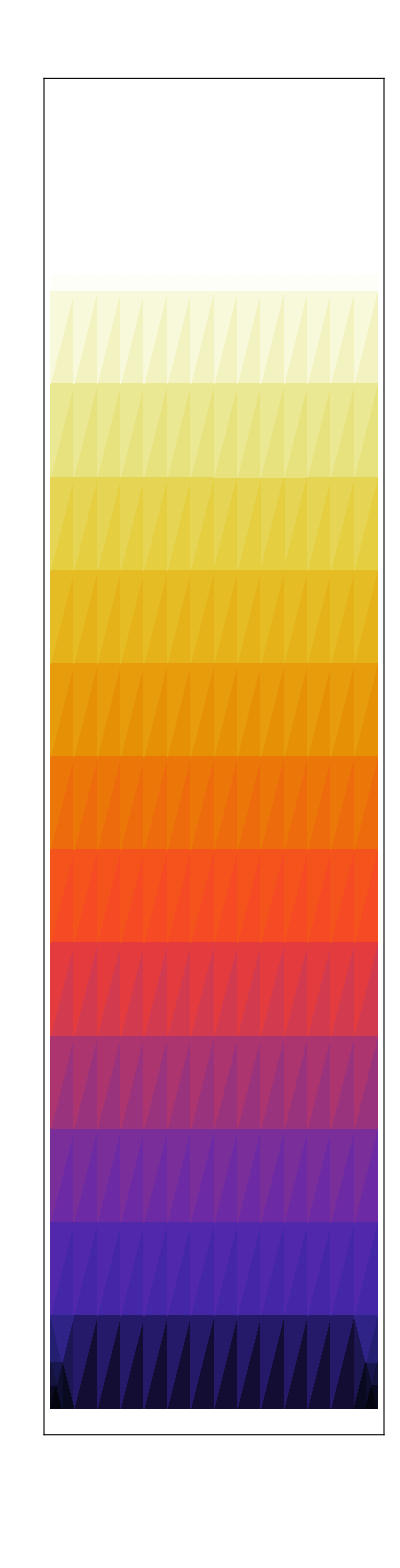

```mathematica
figure8Ilabel=DensityPlot[
y
,{x,0,1},{y,0,1.15figure8Imax}
,PlotRange->{0,figure8Imax}
,ColorFunctionScaling->False
,ColorFunction->Function[CMRwithMin[figure8Imin,2/9][#/figure8Imax]]
,PlotRangePadding->None
,ImageSize->{{600},{figure8Iheight}}
,AspectRatio->20
,FrameTicks->{{None,Join[
{#,Style[PaddedForm[#/4,{2,1}],6],{0.4,0}}&/@Range[0,4,0.8],
{#,"",{0.2,0}}&/@Range[0,5,0.2]
]},{None,None}}
,FrameTicksStyle->Directive[Black]
,ImagePadding->{{1,30},{30,12}}
]
```

#### Ellipses

```mathematica
Unprotect[Power];Power[0.,0]=1;Protect[Power];
ClearAll[EllipseFromChannel]
EllipseFromChannel[np_,nm_,n2_]:=Module[{spin,energy,maxintensity,maxα,lowα,highα,rangeα,centre,semiaxis},
spin=np-nm-n2;
energy=(np+nm)+1.95n2;

maxintensity=(Abs[N@np]^np Abs[N@nm]^Abs[nm])/(Abs[N@np]+Abs[N@nm])^(np+Abs[nm]);
maxα=π/4+ArcTan[√Abs[np],√Abs[nm]];

{lowα,highα}=If[nm==0,{#⟦1⟧,90°-#⟦1⟧},#]&@Sort[Tally[Table[
α/.FindRoot[Cos[α-π/4]^(2Abs[np])Sin[α-π/4]^(2Abs[nm])==1/2 maxintensity,{α,RandomReal[{-40°,40 °}],-40°,40°}]
,{40}],Abs[#1-#2]<10.^-3&]⟦All,1⟧];
centre=(highα+lowα)/2;
semiaxis=(highα-lowα)/2;


Graphics[{
Text[
Style["("<>ToString[np]<>", "<>ToString[nm]<>"; "<>ToString[n2]<>")",White,6,FontWeight->Bold]
,{Max[8°,N@centre+If[nm<0,7.5°,0]],energy+ 0.5}
],
Thickness[0.006],White ,
Tooltip[{
Circle[{N@centre,energy},{N@semiaxis,0.2}],Circle[{90°-N@centre,energy},{N@semiaxis,0.2}]
}
,Column[{"("<>ToString[np]<>","<>ToString[nm]<>","<>ToString[n2]<>")","("<>ToString[np+nm]<>","<>ToString[n2]<>")"}]]}
]
]
Style[
Show[
EllipseFromChannel[5,0,4]/.White->Black
,AspectRatio->1/2
,ImageSize->75
]
,Magnification->3]
```

-Graphics-

```mathematica
channelsList[1]=({{4, 0, 3}, {5, 0, 4}, {6, 0, 5}, {7, 0, 6}, {8, 0, 7}, {4, -1, 4}, {5, -1, 5}, {6, -1, 6}, {7, -1, 7}, {8, -1, 8}, {5, 1, 3}, {6, 1, 4}, {7, 1, 5}, {8, 1, 6}, {6, 3, 2}, {7, 3, 3}, {8, 3, 4}});channelsList[-1]=({{3, 0, 4}, {4, 0, 5}, {5, 0, 6}, {6, 0, 7}, {7, 0, 8}, {3, 1, 3}, {4, 1, 4}, {5, 1, 5}, {6, 1, 6}, {7, 1, 7}, {3, -1, 5}, {4, -1, 6}, {5, -1, 7}, {6, -1, 8}, {4, 3, 2}, {5, 3, 3}, {6, 3, 4}, {7, 3, 5}});
```

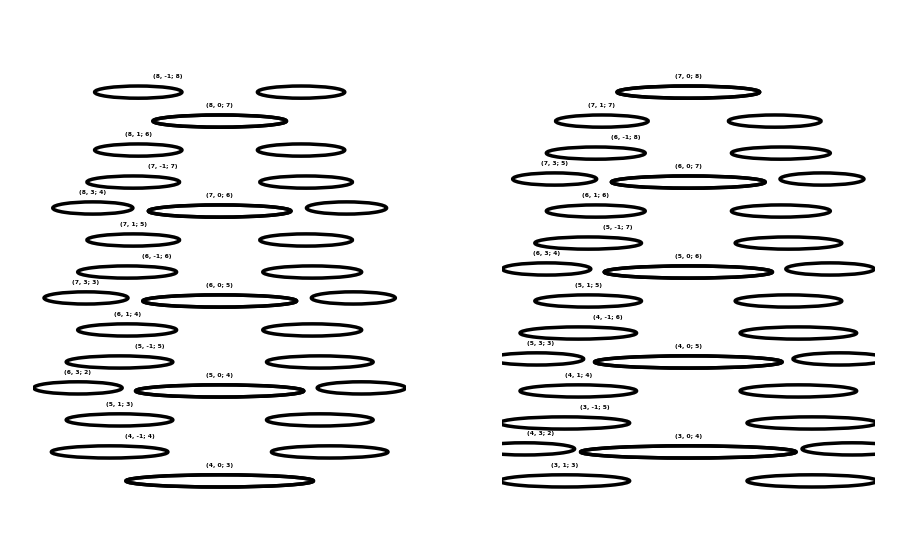
0.647511
-Graphics-

```mathematica
Column@AbsoluteTiming[
GraphicsRow[Table[
ellipseOverlays[ϵ]=Show[
Quiet[EllipseFromChannel@@@channelsList[ϵ]]
,PlotRange->{{0,90°},{9.5,24}}
,ImageSize->420
,AspectRatio->1.2
]
,{ϵ,{1,-1}}]]
]/.White->Black
```

#### Figure

```mathematica
AbsoluteTiming[
Row[Table[
figure8I[ϵ]=Show[{
DensityPlot[
Abs[ellipticityScan[ϵ][HO,α]]
,{α,0,90°},{HO,9.5,24}
,PlotRange->{0,figure8Imax}
,PlotRange->Full

(*,PlotPoints->20,MaxRecursion->3*)

,PlotPoints->60
,MaxRecursion->3
,ColorFunction->CMRwithMin[figure8Imin,2/9]
,PlotRangePadding->None
,ImageSize->{{600},{figure8Iheight}}
,AspectRatio->1.2
,FrameTicks->{{If[ϵ==1,
Join[{#,Style[ToString[#],7,Black],{0.03,0}}&/@Range[12,22,3],{#,"",{0.015,0}}&/@Range[10,22]],
Join[{#,"",{0.03,0}}&/@Range[12,22,3],{#,"",{0.015,0}}&/@Range[10,22]]
]
,Join[{#,"",{0.01,0}}&/@Range[12,22,3],{#,"",{0.005,0}}&/@Range[10,22]]},
{
{# °,Style[ToString[#]<>"°",7,Black],{0.02,0}}&/@Range[0,90,15],{# °,"",{0.02,0}}&/@Range[0,90,15]
}}
,BaseStyle->{Black}
,ImagePadding->{{5+20Boole[ϵ==1],5+38Boole[ϵ==-1]},{30,12}}
,FrameLabel->{MaTeX["\\alpha",FontSize->9],If[ϵ==1,Style["Harmonic order",Black],##&[]]}
,PlotRangeClipping->False
,Epilog->{If[ϵ==-1,{
Inset[figure8Ilabel,ImageScaled[{1.02,0}],ImageScaled[{1,0}]],
Inset[Rotate[Text[Style["Harmonic yield (arb.u.)",7,Black]],90°],ImageScaled[{1,0.5}],Scaled[{1,0.5}]],
Inset[Text[Style["(b) Left-circular",9,Black,FontFamily->"Latin Modern Math"]],Scaled[{0.5,1.01}],Scaled[{0.5,0}]]
},{
Inset[Text[Style["(a) Right-circular",9,Black,FontFamily->"Latin Modern Math"]],Scaled[{0.5,1.01}],Scaled[{0.5,0}]]
}]}
],
ellipseOverlays[ϵ]
}]
,{ϵ,{1,-1}}]];
]
Row[Style[#,Magnification->3]&/@(figure8I/@{1,-1})]
FileByteCount[Export[$OutputDirectory<>"figure8Ia.png",figure8I[1],ImageResolution->300]]
FileByteCount[Export[$OutputDirectory<>"figure8Ib.png",figure8I[-1],ImageResolution->300]]
```

{13.3718,Null}

524434

562139

### Figure 8J - subchannel splittings

#### Initialization

Computer and package conditions used in the calculation

```mathematica
Print[$MachineName]
Print[$RBSFAversion]
Print[$RBSFAcommit]
```

ramanujan

RB-SFA v2.1.1, Wed 8 Jun 2016 15:00:40

commit 2b1760d1bab5f0fcf0a85f5001ca9d1baab4d698
Author: Emilio Pisanty <pisanty@mbi-berlin.de>
Date:   Wed Jun 8 15:39:31 2016 +0200
    Fixes on Verbose returns
    
    Moved to Function[#1... ] for Verboseâ.86.923 to avoid shadowing problems. Fixed shadowing problems on Verboseâ.86.922.

#### Fields

```mathematica
detunedBicircularA[t_]:=((
F2/ω2{Cos[β]Cos[ω2 t-ϕ1],Sin[β]Sin[ω2 t-ϕ1]}+F1/(√2)(1/ω1 Cos[α-π/4]{Cos[ω1 t+ϕ1],-Sin[ω1 t+ϕ1]}+1/((1+δ)ω1)Sin[α-π/4]{Cos[(1+δ)ω1 t-ϕ1+ϕ2],+Sin[(1+δ)ω1 t -ϕ1+ϕ2]})
)flatTopEnvelope[ω1,nTotal,nRamp][t])
detuningParameters={F1->0.075,F2->0.075,α->35°,β->45°,ω1->45.6/800,ω2->45.6/410,nTotal->20,nRamp->2.5,ϕ1->0,ϕ2->0};
figure8Jconditions:=Sequence[TotalCycles->20,CarrierFrequency->45.6/800,PointsPerCycle->100,IntegrationPointsPerCycle->120];
```

Envelope in use:

```mathematica
Block[{ω1=1,nTotal=20,envPower=3},Plot[flatTopEnvelope[ω1,nTotal,envPower][t],{t,0,nTotal (2π)/ω1}]]
```

#### Calculation admin

```mathematica
Quit
```

```mathematica
Length[LaunchKernels[16-Length[Kernels[]]]]
```

16

```mathematica
Length[δRange=Range[0,0.25,0.001]]
```

251

```mathematica
directory=$OutputDirectory<>"/Temp\ Data/";
filename[δ_]:=FileNameJoin[{directory,"detuning scan at delta="<>ToString[N[δ,2]]<>".txt"}]
```

#### Calculation

```mathematica
DateString[]

ParallelTable[
Block[{file,timing},
file=OpenWrite[filename[d]];
timing=First[AbsoluteTiming[makeDipoleList[
VectorPotential->detunedBicircularA
,FieldParameters->Join[detuningParameters,{δ->d}]
,Target->"Argon"
,figure8Jconditions
,Preintegrals->"Numeric"
,ReportingFunction->Function[Write[file,#];]
]]];
Close[file];
Print["Finished with delta="<>ToString[N[d]]<>"° at "<>DateString[]<>" after "<>ToString[timing]<>"s="<>ToString[N[timing/60]]<>"min"];
],{d,δRange}]

DateString[]
```

Sat 3 Sep 2016 00:47:08

Finished with delta=0.° at Sat 3 Sep 2016 00:51:20 after 251.252s=4.18753min

Finished with delta=0.076° at Sat 3 Sep 2016 00:51:27 after 258.26s=4.30434min

Finished with delta=0.066° at Sat 3 Sep 2016 00:51:27 after 258.921s=4.31535min

Finished with delta=0.006° at Sat 3 Sep 2016 00:51:28 after 260.079s=4.33465min

Finished with delta=0.054° at Sat 3 Sep 2016 00:51:28 after 260.096s=4.33494min

Finished with delta=0.048° at Sat 3 Sep 2016 00:51:30 after 261.455s=4.35759min

Finished with delta=0.024° at Sat 3 Sep 2016 00:51:31 after 262.674s=4.3779min

Finished with delta=0.042° at Sat 3 Sep 2016 00:51:31 after 262.971s=4.38286min

Finished with delta=0.012° at Sat 3 Sep 2016 00:51:32 after 264.089s=4.40148min

Finished with delta=0.071° at Sat 3 Sep 2016 00:51:33 after 264.4s=4.40667min

Finished with delta=0.018° at Sat 3 Sep 2016 00:51:33 after 264.497s=4.40829min

Finished with delta=0.086° at Sat 3 Sep 2016 00:51:33 after 265.014s=4.41691min

Finished with delta=0.03° at Sat 3 Sep 2016 00:51:34 after 265.169s=4.41948min

Finished with delta=0.081° at Sat 3 Sep 2016 00:51:34 after 265.568s=4.42613min

Finished with delta=0.06° at Sat 3 Sep 2016 00:51:36 after 267.201s=4.45335min

Finished with delta=0.036° at Sat 3 Sep 2016 00:51:38 after 269.831s=4.49718min

Finished with delta=0.001° at Sat 3 Sep 2016 00:55:38 after 258.723s=4.31205min

Finished with delta=0.077° at Sat 3 Sep 2016 00:55:41 after 253.86s=4.231min

Finished with delta=0.067° at Sat 3 Sep 2016 00:55:45 after 257.829s=4.29716min

Finished with delta=0.049° at Sat 3 Sep 2016 00:55:45 after 255.562s=4.25937min

Finished with delta=0.087° at Sat 3 Sep 2016 00:55:45 after 252.057s=4.20095min

Finished with delta=0.082° at Sat 3 Sep 2016 00:55:46 after 252.14s=4.20234min

Finished with delta=0.007° at Sat 3 Sep 2016 00:55:47 after 258.347s=4.30579min

Finished with delta=0.031° at Sat 3 Sep 2016 00:55:48 after 254.173s=4.23621min

Finished with delta=0.055° at Sat 3 Sep 2016 00:55:48 after 259.888s=4.33147min

Finished with delta=0.019° at Sat 3 Sep 2016 00:55:50 after 257.03s=4.28384min

Finished with delta=0.072° at Sat 3 Sep 2016 00:55:50 after 257.417s=4.29029min

Finished with delta=0.043° at Sat 3 Sep 2016 00:55:51 after 259.216s=4.32026min

Finished with delta=0.061° at Sat 3 Sep 2016 00:55:52 after 256.103s=4.26839min

Finished with delta=0.025° at Sat 3 Sep 2016 00:55:52 after 260.901s=4.34836min

Finished with delta=0.013° at Sat 3 Sep 2016 00:55:54 after 261.076s=4.35127min

Finished with delta=0.037° at Sat 3 Sep 2016 00:55:56 after 257.706s=4.2951min

Finished with delta=0.083° at Sat 3 Sep 2016 00:59:55 after 248.747s=4.14578min

Finished with delta=0.002° at Sat 3 Sep 2016 00:59:58 after 259.627s=4.32711min

Finished with delta=0.05° at Sat 3 Sep 2016 01:00:00 after 254.43s=4.2405min

Finished with delta=0.078° at Sat 3 Sep 2016 01:00:01 after 260.297s=4.33828min

Finished with delta=0.02° at Sat 3 Sep 2016 01:00:04 after 254.417s=4.24028min

Finished with delta=0.026° at Sat 3 Sep 2016 01:00:06 after 254.305s=4.23841min

Finished with delta=0.008° at Sat 3 Sep 2016 01:00:07 after 260.01s=4.3335min

Finished with delta=0.056° at Sat 3 Sep 2016 01:00:07 after 258.465s=4.30775min

Finished with delta=0.032° at Sat 3 Sep 2016 01:00:07 after 259.71s=4.32849min

Finished with delta=0.088° at Sat 3 Sep 2016 01:00:07 after 261.986s=4.36644min

Finished with delta=0.044° at Sat 3 Sep 2016 01:00:08 after 257.069s=4.28448min

Finished with delta=0.068° at Sat 3 Sep 2016 01:00:09 after 264.087s=4.40145min

Finished with delta=0.073° at Sat 3 Sep 2016 01:00:09 after 259.139s=4.31898min

Finished with delta=0.014° at Sat 3 Sep 2016 01:00:10 after 256.137s=4.26896min

Finished with delta=0.062° at Sat 3 Sep 2016 01:00:12 after 260.199s=4.33666min

Finished with delta=0.038° at Sat 3 Sep 2016 01:00:16 after 260.267s=4.33778min

Finished with delta=0.084° at Sat 3 Sep 2016 01:04:12 after 257.263s=4.28771min

Finished with delta=0.079° at Sat 3 Sep 2016 01:04:17 after 256.172s=4.26953min

Finished with delta=0.003° at Sat 3 Sep 2016 01:04:17 after 259.496s=4.32493min

Finished with delta=0.051° at Sat 3 Sep 2016 01:04:20 after 260.382s=4.3397min

Finished with delta=0.021° at Sat 3 Sep 2016 01:04:22 after 257.655s=4.29426min

Finished with delta=0.027° at Sat 3 Sep 2016 01:04:24 after 257.869s=4.29782min

Finished with delta=0.045° at Sat 3 Sep 2016 01:04:25 after 257.326s=4.28876min

Finished with delta=0.074° at Sat 3 Sep 2016 01:04:26 after 256.486s=4.27476min

Finished with delta=0.057° at Sat 3 Sep 2016 01:04:26 after 259.34s=4.32233min

Finished with delta=0.009° at Sat 3 Sep 2016 01:04:26 after 259.62s=4.327min

Finished with delta=0.033° at Sat 3 Sep 2016 01:04:26 after 259.056s=4.3176min

Finished with delta=0.069° at Sat 3 Sep 2016 01:04:28 after 258.766s=4.31276min

Finished with delta=0.089° at Sat 3 Sep 2016 01:04:28 after 260.552s=4.34254min

Finished with delta=0.015° at Sat 3 Sep 2016 01:04:28 after 258.376s=4.30627min

Finished with delta=0.063° at Sat 3 Sep 2016 01:04:30 after 258.15s=4.30249min

Finished with delta=0.039° at Sat 3 Sep 2016 01:04:35 after 258.374s=4.30623min

Finished with delta=0.085° at Sat 3 Sep 2016 01:08:32 after 259.651s=4.32751min

Finished with delta=0.004° at Sat 3 Sep 2016 01:08:33 after 255.812s=4.26353min

Finished with delta=0.08° at Sat 3 Sep 2016 01:08:36 after 259.46s=4.32434min

Finished with delta=0.022° at Sat 3 Sep 2016 01:08:37 after 255.187s=4.25312min

Finished with delta=0.052° at Sat 3 Sep 2016 01:08:37 after 257.157s=4.28595min

Finished with delta=0.016° at Sat 3 Sep 2016 01:08:40 after 252.182s=4.20304min

Finished with delta=0.075° at Sat 3 Sep 2016 01:08:42 after 255.797s=4.26329min

Finished with delta=0.058° at Sat 3 Sep 2016 01:08:44 after 257.497s=4.29161min

Finished with delta=0.034° at Sat 3 Sep 2016 01:08:45 after 258.849s=4.31415min

Finished with delta=0.07° at Sat 3 Sep 2016 01:08:46 after 257.702s=4.29503min

Finished with delta=0.028° at Sat 3 Sep 2016 01:08:46 after 262.08s=4.368min

Finished with delta=0.046° at Sat 3 Sep 2016 01:08:47 after 262.282s=4.37137min

Finished with delta=0.01° at Sat 3 Sep 2016 01:08:47 after 260.976s=4.3496min

Finished with delta=0.09° at Sat 3 Sep 2016 01:08:49 after 261.09s=4.35151min

Finished with delta=0.064° at Sat 3 Sep 2016 01:08:50 after 259.738s=4.32896min

Finished with delta=0.04° at Sat 3 Sep 2016 01:08:51 after 256.075s=4.26791min

Finished with delta=0.017° at Sat 3 Sep 2016 01:12:51 after 250.456s=4.17427min

Finished with delta=0.005° at Sat 3 Sep 2016 01:12:53 after 259.68s=4.328min

Finished with delta=0.091° at Sat 3 Sep 2016 01:12:54 after 261.933s=4.36555min

Finished with delta=0.053° at Sat 3 Sep 2016 01:12:57 after 259.872s=4.3312min

Finished with delta=0.096° at Sat 3 Sep 2016 01:12:57 after 260.78s=4.34633min

Finished with delta=0.023° at Sat 3 Sep 2016 01:12:57 after 260.253s=4.33755min

Finished with delta=0.047° at Sat 3 Sep 2016 01:13:01 after 254.03s=4.23383min

Finished with delta=0.059° at Sat 3 Sep 2016 01:13:02 after 258.701s=4.31168min

Finished with delta=0.101° at Sat 3 Sep 2016 01:13:03 after 261.13s=4.35216min

Finished with delta=0.106° at Sat 3 Sep 2016 01:13:03 after 257.125s=4.28542min

Finished with delta=0.029° at Sat 3 Sep 2016 01:13:03 after 257.005s=4.28342min

Finished with delta=0.041° at Sat 3 Sep 2016 01:13:05 after 254.551s=4.24252min

Finished with delta=0.011° at Sat 3 Sep 2016 01:13:05 after 257.849s=4.29748min

Finished with delta=0.035° at Sat 3 Sep 2016 01:13:06 after 260.548s=4.34246min

Finished with delta=0.065° at Sat 3 Sep 2016 01:13:06 after 256.543s=4.27572min

Finished with delta=0.111° at Sat 3 Sep 2016 01:13:13 after 264.208s=4.40347min

Finished with delta=0.116° at Sat 3 Sep 2016 01:17:08 after 257.628s=4.29379min

Finished with delta=0.097° at Sat 3 Sep 2016 01:17:10 after 252.867s=4.21446min

Finished with delta=0.092° at Sat 3 Sep 2016 01:17:13 after 258.886s=4.31477min

Finished with delta=0.131° at Sat 3 Sep 2016 01:17:14 after 256.268s=4.27113min

Finished with delta=0.126° at Sat 3 Sep 2016 01:17:15 after 258.071s=4.30118min

Finished with delta=0.121° at Sat 3 Sep 2016 01:17:16 after 262.938s=4.3823min

Finished with delta=0.151° at Sat 3 Sep 2016 01:17:19 after 253.445s=4.22408min

Finished with delta=0.136° at Sat 3 Sep 2016 01:17:19 after 257.658s=4.29431min

Finished with delta=0.102° at Sat 3 Sep 2016 01:17:19 after 256.424s=4.27374min

Finished with delta=0.141° at Sat 3 Sep 2016 01:17:21 after 258.437s=4.30728min

Finished with delta=0.107° at Sat 3 Sep 2016 01:17:21 after 258.091s=4.30151min

Finished with delta=0.146° at Sat 3 Sep 2016 01:17:22 after 258.405s=4.30675min

Finished with delta=0.156° at Sat 3 Sep 2016 01:17:23 after 257.973s=4.29956min

Finished with delta=0.161° at Sat 3 Sep 2016 01:17:27 after 261.463s=4.35772min

Finished with delta=0.166° at Sat 3 Sep 2016 01:17:28 after 261.974s=4.36623min

Finished with delta=0.112° at Sat 3 Sep 2016 01:17:35 after 261.203s=4.35338min

Finished with delta=0.098° at Sat 3 Sep 2016 01:21:26 after 255.546s=4.2591min

Finished with delta=0.117° at Sat 3 Sep 2016 01:21:27 after 258.82s=4.31367min

Finished with delta=0.132° at Sat 3 Sep 2016 01:21:32 after 257.948s=4.29913min

Finished with delta=0.127° at Sat 3 Sep 2016 01:21:33 after 257.51s=4.29184min

Finished with delta=0.142° at Sat 3 Sep 2016 01:21:33 after 252.168s=4.2028min

Finished with delta=0.093° at Sat 3 Sep 2016 01:21:35 after 262.348s=4.37247min

Finished with delta=0.137° at Sat 3 Sep 2016 01:21:35 after 256.375s=4.27292min

Finished with delta=0.152° at Sat 3 Sep 2016 01:21:38 after 259.523s=4.32538min

Finished with delta=0.122° at Sat 3 Sep 2016 01:21:38 after 262.54s=4.37566min

Finished with delta=0.157° at Sat 3 Sep 2016 01:21:41 after 257.271s=4.28785min

Finished with delta=0.108° at Sat 3 Sep 2016 01:21:42 after 260.701s=4.34501min

Finished with delta=0.147° at Sat 3 Sep 2016 01:21:42 after 260.828s=4.34713min

Finished with delta=0.162° at Sat 3 Sep 2016 01:21:43 after 255.661s=4.26101min

Finished with delta=0.103° at Sat 3 Sep 2016 01:21:43 after 263.987s=4.39979min

Finished with delta=0.167° at Sat 3 Sep 2016 01:21:48 after 260.088s=4.33481min

Finished with delta=0.113° at Sat 3 Sep 2016 01:21:49 after 254.12s=4.23533min

Finished with delta=0.099° at Sat 3 Sep 2016 01:25:40 after 254.037s=4.23394min

Finished with delta=0.133° at Sat 3 Sep 2016 01:25:47 after 254.825s=4.24708min

Finished with delta=0.118° at Sat 3 Sep 2016 01:25:47 after 260.285s=4.33808min

Finished with delta=0.094° at Sat 3 Sep 2016 01:25:49 after 253.705s=4.22841min

Finished with delta=0.143° at Sat 3 Sep 2016 01:25:51 after 257.93s=4.29883min

Finished with delta=0.153° at Sat 3 Sep 2016 01:25:54 after 255.92s=4.26534min

Finished with delta=0.128° at Sat 3 Sep 2016 01:25:54 after 261.183s=4.35305min

Finished with delta=0.138° at Sat 3 Sep 2016 01:25:54 after 258.889s=4.31482min

Finished with delta=0.123° at Sat 3 Sep 2016 01:25:56 after 257.58s=4.293min

Finished with delta=0.148° at Sat 3 Sep 2016 01:25:56 after 253.895s=4.23158min

Finished with delta=0.109° at Sat 3 Sep 2016 01:25:59 after 256.912s=4.28187min

Finished with delta=0.158° at Sat 3 Sep 2016 01:26:00 after 259.152s=4.31921min

Finished with delta=0.104° at Sat 3 Sep 2016 01:26:03 after 259.426s=4.32376min

Finished with delta=0.163° at Sat 3 Sep 2016 01:26:04 after 261.459s=4.35766min

Finished with delta=0.114° at Sat 3 Sep 2016 01:26:13 after 264.308s=4.40513min

Finished with delta=0.168° at Sat 3 Sep 2016 01:26:13 after 264.675s=4.41126min

Finished with delta=0.1° at Sat 3 Sep 2016 01:29:48 after 248.742s=4.1457min

Finished with delta=0.119° at Sat 3 Sep 2016 01:29:58 after 250.049s=4.16748min

Finished with delta=0.134° at Sat 3 Sep 2016 01:30:02 after 255.371s=4.25619min

Finished with delta=0.095° at Sat 3 Sep 2016 01:30:09 after 259.956s=4.3326min

Finished with delta=0.144° at Sat 3 Sep 2016 01:30:10 after 258.85s=4.31417min

Finished with delta=0.139° at Sat 3 Sep 2016 01:30:12 after 258.06s=4.30101min

Finished with delta=0.159° at Sat 3 Sep 2016 01:30:13 after 252.969s=4.21615min

Finished with delta=0.149° at Sat 3 Sep 2016 01:30:13 after 256.928s=4.28214min

Finished with delta=0.129° at Sat 3 Sep 2016 01:30:16 after 261.631s=4.36051min

Finished with delta=0.154° at Sat 3 Sep 2016 01:30:17 after 263.089s=4.38482min

Finished with delta=0.124° at Sat 3 Sep 2016 01:30:17 after 261.306s=4.3551min

Finished with delta=0.11° at Sat 3 Sep 2016 01:30:18 after 259.109s=4.31849min

Finished with delta=0.105° at Sat 3 Sep 2016 01:30:19 after 256.683s=4.27805min

Finished with delta=0.164° at Sat 3 Sep 2016 01:30:22 after 257.896s=4.29827min

Finished with delta=0.169° at Sat 3 Sep 2016 01:30:34 after 260.58s=4.343min

Finished with delta=0.115° at Sat 3 Sep 2016 01:30:36 after 262.988s=4.38313min

Finished with delta=0.171° at Sat 3 Sep 2016 01:34:12 after 263.557s=4.39262min

Finished with delta=0.12° at Sat 3 Sep 2016 01:34:14 after 256.945s=4.28241min

Finished with delta=0.135° at Sat 3 Sep 2016 01:34:19 after 257.258s=4.28763min

Finished with delta=0.14° at Sat 3 Sep 2016 01:34:28 after 255.561s=4.25935min

Finished with delta=0.125° at Sat 3 Sep 2016 01:34:28 after 250.741s=4.17901min

Finished with delta=0.176° at Sat 3 Sep 2016 01:34:30 after 260.961s=4.34935min

Finished with delta=0.186° at Sat 3 Sep 2016 01:34:30 after 250.998s=4.18329min

Finished with delta=0.145° at Sat 3 Sep 2016 01:34:31 after 261.128s=4.35213min

Finished with delta=0.15° at Sat 3 Sep 2016 01:34:31 after 257.85s=4.2975min

Finished with delta=0.155° at Sat 3 Sep 2016 01:34:34 after 256.805s=4.28008min

Finished with delta=0.16° at Sat 3 Sep 2016 01:34:34 after 261.653s=4.36089min

Finished with delta=0.13° at Sat 3 Sep 2016 01:34:37 after 261.638s=4.36063min

Finished with delta=0.181° at Sat 3 Sep 2016 01:34:39 after 261.489s=4.35815min

Finished with delta=0.165° at Sat 3 Sep 2016 01:34:43 after 260.652s=4.3442min

Finished with delta=0.191° at Sat 3 Sep 2016 01:34:53 after 256.741s=4.27902min

Finished with delta=0.17° at Sat 3 Sep 2016 01:34:56 after 261.831s=4.36385min

Finished with delta=0.196° at Sat 3 Sep 2016 01:38:28 after 253.387s=4.22312min

Finished with delta=0.201° at Sat 3 Sep 2016 01:38:33 after 253.902s=4.23169min

Finished with delta=0.172° at Sat 3 Sep 2016 01:38:36 after 263.851s=4.39751min

Finished with delta=0.221° at Sat 3 Sep 2016 01:38:44 after 253.309s=4.22182min

Finished with delta=0.187° at Sat 3 Sep 2016 01:38:45 after 254.592s=4.24321min

Finished with delta=0.231° at Sat 3 Sep 2016 01:38:45 after 251.04s=4.184min

Finished with delta=0.177° at Sat 3 Sep 2016 01:38:47 after 257.437s=4.29061min

Finished with delta=0.206° at Sat 3 Sep 2016 01:38:48 after 260.426s=4.34044min

Finished with delta=0.216° at Sat 3 Sep 2016 01:38:50 after 259.222s=4.32036min

Finished with delta=0.211° at Sat 3 Sep 2016 01:38:52 after 263.482s=4.39137min

Finished with delta=0.226° at Sat 3 Sep 2016 01:38:53 after 258.877s=4.31462min

Finished with delta=0.236° at Sat 3 Sep 2016 01:38:56 after 258.278s=4.30463min

Finished with delta=0.182° at Sat 3 Sep 2016 01:39:03 after 263.631s=4.39386min

Finished with delta=0.241° at Sat 3 Sep 2016 01:39:06 after 262.705s=4.37842min

Finished with delta=0.192° at Sat 3 Sep 2016 01:39:11 after 258.051s=4.30085min

Finished with delta=0.246° at Sat 3 Sep 2016 01:39:14 after 258.537s=4.30895min

Finished with delta=0.202° at Sat 3 Sep 2016 01:42:46 after 252.435s=4.20725min

Finished with delta=0.197° at Sat 3 Sep 2016 01:42:48 after 260.577s=4.34295min

Finished with delta=0.188° at Sat 3 Sep 2016 01:42:56 after 251.012s=4.18353min

Finished with delta=0.173° at Sat 3 Sep 2016 01:42:56 after 260.332s=4.33887min

Finished with delta=0.222° at Sat 3 Sep 2016 01:43:01 after 256.683s=4.27805min

Finished with delta=0.232° at Sat 3 Sep 2016 01:43:03 after 257.27s=4.28783min

Finished with delta=0.178° at Sat 3 Sep 2016 01:43:05 after 258.072s=4.30119min

Finished with delta=0.217° at Sat 3 Sep 2016 01:43:09 after 258.511s=4.30852min

Finished with delta=0.207° at Sat 3 Sep 2016 01:43:10 after 261.626s=4.36043min

Finished with delta=0.212° at Sat 3 Sep 2016 01:43:10 after 258.455s=4.30758min

Finished with delta=0.237° at Sat 3 Sep 2016 01:43:11 after 255.281s=4.25468min

Finished with delta=0.227° at Sat 3 Sep 2016 01:43:12 after 259.042s=4.31737min

Finished with delta=0.183° at Sat 3 Sep 2016 01:43:23 after 260.619s=4.34365min

Finished with delta=0.242° at Sat 3 Sep 2016 01:43:24 after 258.358s=4.30596min

Finished with delta=0.193° at Sat 3 Sep 2016 01:43:32 after 260.74s=4.34567min

Finished with delta=0.247° at Sat 3 Sep 2016 01:43:37 after 262.894s=4.38157min

Finished with delta=0.203° at Sat 3 Sep 2016 01:46:55 after 249.418s=4.15696min

Finished with delta=0.198° at Sat 3 Sep 2016 01:47:01 after 252.69s=4.21151min

Finished with delta=0.189° at Sat 3 Sep 2016 01:47:11 after 255.543s=4.25905min

Finished with delta=0.174° at Sat 3 Sep 2016 01:47:13 after 256.867s=4.28111min

Finished with delta=0.179° at Sat 3 Sep 2016 01:47:15 after 250.351s=4.17252min

Finished with delta=0.223° at Sat 3 Sep 2016 01:47:17 after 255.557s=4.25929min

Finished with delta=0.233° at Sat 3 Sep 2016 01:47:20 after 257.13s=4.28551min

Finished with delta=0.208° at Sat 3 Sep 2016 01:47:26 after 256.245s=4.27075min

Finished with delta=0.218° at Sat 3 Sep 2016 01:47:30 after 261.042s=4.35069min

Finished with delta=0.213° at Sat 3 Sep 2016 01:47:32 after 262.s=4.36667min

Finished with delta=0.238° at Sat 3 Sep 2016 01:47:35 after 263.521s=4.39201min

Finished with delta=0.228° at Sat 3 Sep 2016 01:47:36 after 264.514s=4.40857min

Finished with delta=0.184° at Sat 3 Sep 2016 01:47:40 after 257.02s=4.28366min

Finished with delta=0.243° at Sat 3 Sep 2016 01:47:44 after 259.514s=4.32523min

Finished with delta=0.194° at Sat 3 Sep 2016 01:47:53 after 261.981s=4.36635min

Finished with delta=0.248° at Sat 3 Sep 2016 01:47:57 after 260.077s=4.33462min

Finished with delta=0.204° at Sat 3 Sep 2016 01:51:07 after 252.184s=4.20307min

Finished with delta=0.199° at Sat 3 Sep 2016 01:51:19 after 258.238s=4.30397min

Finished with delta=0.19° at Sat 3 Sep 2016 01:51:30 after 258.557s=4.30928min

Finished with delta=0.175° at Sat 3 Sep 2016 01:51:33 after 259.521s=4.32535min

Finished with delta=0.224° at Sat 3 Sep 2016 01:51:33 after 256.716s=4.2786min

Finished with delta=0.18° at Sat 3 Sep 2016 01:51:33 after 257.999s=4.29998min

Finished with delta=0.234° at Sat 3 Sep 2016 01:51:38 after 258.03s=4.3005min

Finished with delta=0.209° at Sat 3 Sep 2016 01:51:39 after 252.594s=4.2099min

Finished with delta=0.219° at Sat 3 Sep 2016 01:51:45 after 255.604s=4.26006min

Finished with delta=0.214° at Sat 3 Sep 2016 01:51:50 after 258.366s=4.30611min

Finished with delta=0.229° at Sat 3 Sep 2016 01:51:53 after 256.05s=4.2675min

Finished with delta=0.239° at Sat 3 Sep 2016 01:51:53 after 258.067s=4.30111min

Finished with delta=0.185° at Sat 3 Sep 2016 01:51:55 after 254.444s=4.24073min

Finished with delta=0.244° at Sat 3 Sep 2016 01:51:59 after 255.808s=4.26347min

Finished with delta=0.195° at Sat 3 Sep 2016 01:52:05 after 251.696s=4.19493min

Finished with delta=0.249° at Sat 3 Sep 2016 01:52:13 after 256.156s=4.26926min

Finished with delta=0.205° at Sat 3 Sep 2016 01:54:43 after 215.579s=3.59298min

Finished with delta=0.225° at Sat 3 Sep 2016 01:54:59 after 205.548s=3.4258min

Finished with delta=0.235° at Sat 3 Sep 2016 01:55:01 after 203.53s=3.39216min

Finished with delta=0.215° at Sat 3 Sep 2016 01:55:10 after 199.937s=3.33228min

Finished with delta=0.22° at Sat 3 Sep 2016 01:55:11 after 205.879s=3.43131min

Finished with delta=0.23° at Sat 3 Sep 2016 01:55:17 after 204.47s=3.40784min

Finished with delta=0.24° at Sat 3 Sep 2016 01:55:21 after 207.963s=3.46606min

Finished with delta=0.245° at Sat 3 Sep 2016 01:55:22 after 202.9s=3.38166min

Finished with delta=0.25° at Sat 3 Sep 2016 01:55:34 after 200.881s=3.34801min

Finished with delta=0.2° at Sat 3 Sep 2016 01:56:28 after 309.014s=5.15023min

Finished with delta=0.21° at Sat 3 Sep 2016 01:56:48 after 308.735s=5.14558min

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

Sat 3 Sep 2016 01:56:48

#### Data admin

```mathematica
Do[results[δ]=ReadList[filename[δ]],{δ,δRange}]
```

```mathematica
results[0.]
```

{{0.+0. ⅈ,0.+0. ⅈ},{9.54931×10^-14-1.87623×10^-11 ⅈ,-4.95488×10^-16+7.87885×10^-14 ⅈ},{4.19389×10^-12-5.92523×10^-10 ⅈ,-4.71379×10^-14+5.04575×10^-12 ⅈ},{2.84965×10^-11-4.38881×10^-9 ⅈ,-4.96777×10^-13+5.73661×10^-11 ⅈ},3593,{9.22503×10^-6-6.99013×10^-6 ⅈ,-2.01036×10^-6-2.64495×10^-6 ⅈ},{6.11481×10^-6-9.52539×10^-6 ⅈ,-2.74228×10^-6-1.49524×10^-6 ⅈ},{2.42033×10^-6-0.0000107917 ⅈ,-2.99567×10^-6-2.26537×10^-7 ⅈ},{-1.37906×10^-6-0.0000107079 ⅈ,-2.78658×10^-6+9.94105×10^-7 ⅈ}}
 |  |  |  |

```mathematica
Save[$OutputDirectory<>"/figure 8J data.txt",results]
```

To load the data use the entry below:

```mathematica
<<($OutputDirectory<>"figure 8J data.txt");
```

```mathematica
Show[
biColorSpectrum[Most[results[0.2]],ωPower->2,figure8Iconditions,PlotLabel->"Plot to test the data loaded correctly"]
,PlotRange->{{0,90},{-14,-2}}
,GridLines->{Join[Table[n+1.95(n-1),{n,0,40}],Table[n+1.95(n+1),{n,0,20}]],None}
]
```

#### Interpolation

```mathematica
AbsoluteTiming[
Table[
detuningInterpolation[ϵ]=Interpolation[
Flatten[Table[
{{#1,#2},#3}&@@@Transpose[
{harmonicOrderAxis[figure8Jconditions],
ConstantArray[δ,1/2 TotalCycles PointsPerCycle+1/.{figure8Jconditions}],
Log10[
harmonicOrderAxis[figure8Jconditions]^4×
Part[
Abs[({1,ϵ ⅈ}.#)/(√(1+Abs[ϵ]^2))]^2&/@(
Transpose[Fourier/@Transpose[
Re[Most[results[δ]]]
]]
)
,1;;(1/2 TotalCycles PointsPerCycle+1/.{figure8Jconditions})]
]
}]
,{δ,δRange}],1]
]
,{ϵ,{-1,1}}]
]
```

{13.6994,{InterpolatingFunction[{{0., 50.}, {0., 0.25}}, <>],InterpolatingFunction[{{0., 50.}, {0., 0.25}}, <>]}}

Plot to test the interpolation:

```mathematica
Plot[
detuningInterpolation[1][HO,0.12345]
,{HO,0,50}
,PlotRange->Full
,Frame->True
]
```

#### Figure drafts and other scratch

```mathematica
Plot3D[
detuningInterpolation[1][HO,δ]
,{δ,0,0.25},{HO,11.25,18.5}
,PlotRange->{-2.5,1.25}
,PlotRange->Full
,PlotPoints->40
(*,MaxRecursion->4*)
]
```

#### Label

```mathematica
figure8Jheight=240;
figure8Jmax=3;
figure8Jmin=0.015;
```

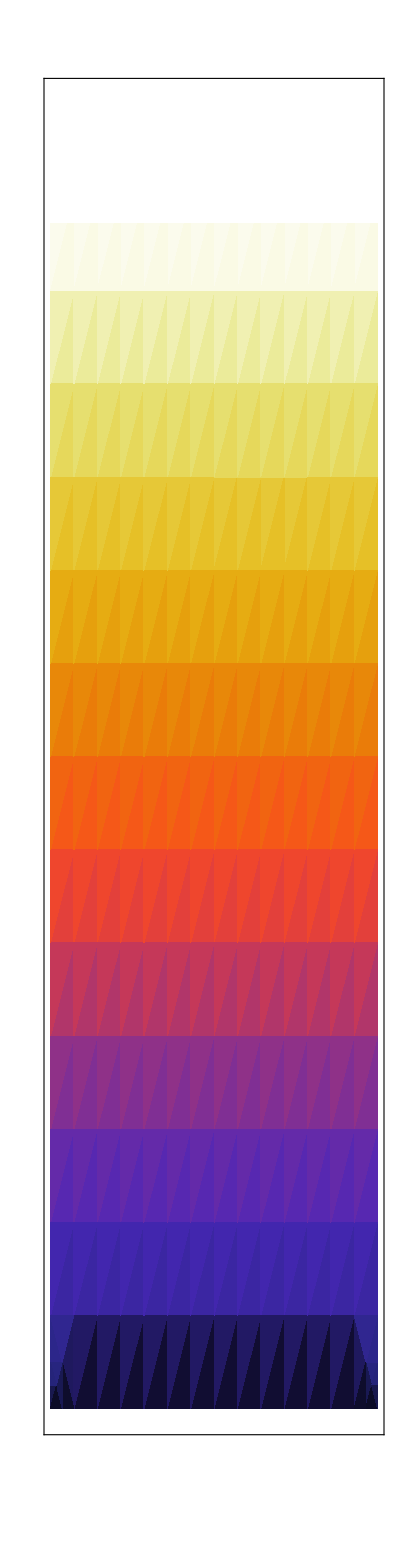

```mathematica
figure8Jlabel=DensityPlot[
y
,{x,0,1},{y,0,1.1figure8Jmax}
,PlotRange->{0,figure8Jmax}
,ColorFunction->CMRwithMin[figure8Jmin]
,PlotRangePadding->None
,ImageSize->{{600},{figure8Iheight}}
,AspectRatio->20
,FrameTicks->{{None,Join[
{#,Style[PaddedForm[#/figure8Jmax,{2,1}],6],{0.4,0}}&/@Range[0,3,0.6],
{#,"",{0.2,0}}&/@Range[0,5,0.12]
]},{None,None}}
,FrameTicksStyle->Directive[Black]
,ImagePadding->{{1,30},{3,3}}
(*,ImagePadding->{{1,30},{40,12}}*)
]
```

#### Channel markings

```mathematica
channelLine[np_,nm_,n2_,OptionsPattern[offset->{0,0}]]:=Show[
Graphics[{Text[
Style[
"("<>ToString[np]<>","<>ToString[nm]<>";"<>ToString[n2]<>")"
,6,White,FontWeight->Bold]
,{0.125,np+1.125nm+1.95n2+0.1},{1.35,1}OptionValue[offset],{1,0.05nm}
]}]
]
channelsList[1]={
{7,1,5,offset->{-4.75,-0.8}},
(*{6,-2,7,offset->{-2.5,-0.5}},*)
{8,5,2,offset->{4.75,-1.5}},
{7,2,4,offset->{1.0,-0.5}},
{6,-1,6,offset->{-3.75,-0.8}},
{6,0,5,offset->{-4.5,-0.8}},
{7,3,3,offset->{4.75,-0.8}},
{7,4,2,offset->{4.75,-1.}},
{5,-3,7,offset->{-1.5,-0.8}},
{6,1,4,offset->{-5.,-0.8}},
(*{7,5,1,offset->{4.75,-1.5}},*)
{5,-2,6,offset->{-1.5,-0.5}},
{6,2,3,offset->{1.0,-0.5}},
{5,-1,5,offset->{-3.75,-0.8}},
{6,3,2,offset->{4.75,-1}},
{5,0,4,offset->{-4.5,-0.8}},
(*{4,-3,6,offset->{-2.5,-0.8}},*)
{5,1,3,offset->{4.75,-0.5}},
{4,-2,5,offset->{-2.,-0.5}}};
channelsList[-1]={
{6,2,5,offset->{1.45,-0.5}},
{5,-1,7,offset->{1-4.75,-0.8}},
{7,6,2,offset->{4.5,-1.6}},
(*{6,3,4,offset->{1.6,-0.5}},*)
{5,0,6,offset->{1-5.5,-0.5}},
(*{4,-3,8,offset->{-2.,-0.8}},*)
{7,7,1,offset->{4.4,-1.6}},
{5,1,5,offset->{1.75,-0.5}},
{4,-2,7,offset->{-2.5,-0.8}},
{5,2,4,offset->{4.5,-0.8}},
{4,-1,6,offset->{1-4.75,-0.8}},
(*{5,3,3,offset->{1.5,-0.8}},*)
{4,0,5,offset->{1-5.5,-0.5}},
{5,4,2,offset->{4.5,-0.8}},
{4,1,4,offset->{1-5.5,-0.5}},
{3,-2,6,offset->{1-3.25,-0.8}},
{4,2,3,offset->{1.45,-0.5}},
{3,-1,5,offset->{1-4.75,-0.8}}
};
channelsImage[ϵ_]:=Show[
channelLine@@@channelsList[ϵ]
(*bounding box:*)(*~Join~{Graphics[{Thickness[0.01],Line[{{0,11.25},{0.25,11.25},{0.25,18.5},{0,18.5},{0,11.25}}]}]}*)
,PlotRange->{{0,0.25},{11.25,18.5}}
,AspectRatio->1.2
,PlotRangePadding->None
,ImagePadding->None
,ImageSize->{Automatic,550}
];
(*Row[Table[
Style[
splittingsImage[ϵ]=Show[
{figure8J[ϵ],
channelsImage[ϵ]}
(*,ImageSize->750*)
]
,Magnification->3]
,{ϵ,{(*1,*)-1}}]
]*)
(*FileByteCount[Export[$OutputDirectory<>"figure8Ja.png",splittingsImage[1],ImageResolution->300]]
FileByteCount[Export[$OutputDirectory<>"figure8Jb.png",splittingsImage[-1],ImageResolution->300]]*)
```

#### Figure

```mathematica
DateString[]
AbsoluteTiming[
Row[Table[
figure8J[ϵ]=Show[{
RegionPlot[
True
,{δ,0,0.25},{HO,11.25,18.5}


,ColorFunction->Function[{δ,HO},CMRwithMin[figure8Jmin][(10^detuningInterpolation[ϵ][HO,δ])/figure8Jmax]]
,ColorFunctionScaling->False

(*,PlotPoints->20*)
,PlotPoints->1200
,PlotPoints->300


,PlotRangePadding->None 
,ImageSize->{{600},{figure8Jheight}}
,AspectRatio->1.2
,FrameTicks->{{If[ϵ==1,
Join[{#,Style[ToString[#],7,Black],{0.03,0}}&/@Range[12,18,1],{#,"",{0.015,0}}&/@Range[10,22,0.25]],
Join[{#,"",{0.03,0}}&/@Range[12,18,1],{#,"",{0.015,0}}&/@Range[10,22,0.25]]
]
,Join[{#,"",{0.01,0}}&/@Range[12,22,1],{#,"",{0.005,0}}&/@Range[10,22,0.25]]},
{
Join[{# ,Style[ToString[#],7,Black],{0.02,0}}&/@Range[0,0.25,0.05],{# ,"",{0.01,0}}&/@Range[0,0.25,0.01]],
Join[{# ,"",{0.02,0}}&/@Range[0,0.25,0.05],{# ,"",{0.01,0}}&/@Range[0,0.25,0.01]]
}}
,BoundaryStyle->None
,BaseStyle->{Black}
,ImagePadding->{{5+20Boole[ϵ==1],8+38Boole[ϵ==-1]},{40,12}}
,FrameLabel->{MaTeX["\\frac{\\omega'}{\\omega}-1",FontSize->9],If[ϵ==1,Style["Harmonic order",Black],##&[]]}
,PlotRangeClipping->False
,Epilog->{If[ϵ==-1,{
Inset[figure8Jlabel,Scaled[{1.05,0}],Scaled[{0,0}],{Automatic,7.5}],
Inset[Rotate[Text[Style["Harmonic yield (arb.u.)",7,Black]],90°],ImageScaled[{1,0.5}],Scaled[{1,0.5}]],
Inset[Text[Style["(b) Left-circular",9,Black,FontFamily->"Latin Modern Math"]],Scaled[{0.5,1.01}],Scaled[{0.5,0}]]
},{
Inset[Text[Style["(a) Right-circular",9,Black,FontFamily->"Latin Modern Math"]],Scaled[{0.5,1.01}],Scaled[{0.5,0}]]
}]}
]
,channelsImage[ϵ]
}]
,{ϵ,{(*1,*)-1}}]];
]
Row[Style[figure8J[#],Magnification->1]&/@{1,-1}]
FileByteCount[Export[$OutputDirectory<>"figure8Ja.png",figure8J[1],ImageResolution->400]]
FileByteCount[Export[$OutputDirectory<>"figure8Jb.png",figure8J[-1],ImageResolution->400]]
DateString[]
```

Wed 26 Oct 2016 20:05:19

{90.2393,Null}

734659

687654

Wed 26 Oct 2016 20:07:19

3D plot to test the vertical scale

```mathematica
Plot3D[
10^detuningInterpolation[1][HO,δ]
,{δ,0,0.25},{HO,11.25,18.5}
,PlotRange->{0,5}
,PlotRange->Full
,PlotPoints->40
(*,MaxRecursion->4*)
,ImageSize->800
]
```